## As a check for diffusion, let’s solve the 2-D diffusion/deformation problem here!

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
A = 5.0*10^-4
D0 =5.4*10^-7
Q = 53.9*10^3
R = 8.314
T = 300.
Diff = D0*Exp[-Q/R/T]
Na = 6.0221413 *10^23;
clinit = 38.7
VM = 7.116 * 10^-6;
NL =1.405283867341203*10^5
WB = 9.65 * 10^3
KT =  Exp[WB/R/T]
NT = 1.0*10^(26.6-1.5*Exp[-0.0*ep])/Na  /. {ep -> 0.}
CT = NT/(1+NL/KT/CL)
dCTdCL = D[CT,CL]
dCTdCLinit = dCTdCL /. {CL -> clinit}
Deff = 1.+dCTdCLinit 


bulkMod = 163.33333333333333*10^9
shearMod = 7.538461538461539*10^10
sig11 = 0.838083*10^9
(*B = (sig11 / 10000. - (bulkMod + 4./3.*shearMod)*A )/ (bulkMod - 2./3. * shearMod)*)
B = 0
```

0.0005

5.4×10^-7

53900.

8.314

300.

2.22449×10^-16

38.7

140528.

9650.

47.8933

20.9049

20.9049/(1+2934.2/CL)

61339.2/((1+2934.2/CL)^2 CL^2)

0.00694031

1.00694

1.63333×10^11

7.53846×10^10

8.38083×10^8

0

```mathematica
NT
```

20.9049

Let’s now specify a deformation gradient and incorporate it into the transport equation - we consider a uniaxial deformation where x1 = X1 + A*t*X1, where the displacement is A*t*X1
Also, x2 = X2 + B*t*X2, where B*t* X2 is the displacement in the X2 direction (based off of the assumption of linear isotropic elasticity).

```mathematica
x1 = X1 + A*t*X1
x2 = X2 + B*t*X2
x3 = X3
F = {{D[x1,X1],D[x1,X2],D[x1,X3]},{D[x2,X1],D[x2,X2],D[x2,X3]},{D[x3,X1],D[x3,X2],D[x3,X3]}}
Finverse = Inverse[F]
```

X1+0.0005 t X1

X2

X3

{{1+0.0005 t,0,0},{0,1,0},{0,0,1}}

{{1/(1+0.0005 t),0,0},{0,1,0},{0,0,1}}

```mathematica
pdecleval = (Diff/Deff)*Finverse[[1,1]]^2*D[cl[X,t],X,X] - D[cl[X,t],t]
```

-cl^(0,1)[X,t]+(2.20916×10^-16 cl^(2,0)[X,t])/(1+0.0005 t)^2

```mathematica
pdeclsolve = NDSolve[{pdecleval == 0, cl[X,0]==clinit,cl[1*10^-6,t] == clinit, cl[0,t]==clinit*(1.+0.0013470284237726098191214470284237726098191214470284*t)},cl,{X,0,1*10^-6},{t,0,10000}, MaxStepSize -> 100]

clFinalTime = 2050;
increment = 20;
clfinal =560;
EvalCl = ConstantArray[0.0,100];
lengthFraction = 1./20. * 10^-6;
For[i=0,i<101,i++,
a = (clfinal - clinit)/clFinalTime;
Solution = NDSolve[{pdecleval == 0, cl[X,0]==clinit,cl[1*10^-6,t] == clinit, cl[0,t]==clinit+a*t},cl,{X,0,1*10^-6},{t,0,10000}, MaxStepSize -> 50];
EvalCl[[i]] = Evaluate[cl[lengthFraction,clFinalTime]/.Solution];
clFinalTime -= increment;
]

EvalCl
```

{{cl→                                 -6
InterpolatingFunction[{{0., 1. 10  }, {0., 10000.}}, <>]}}

{485.223}[{485.184},{485.143},{485.1},{485.056},{485.009},{484.959},{484.907},{484.853},{484.797},{484.737},{484.675},{484.611},{484.543},{484.473},{484.4},{484.323},{484.244},{484.161},{484.075},{483.985},{483.891},{483.794},{483.693},{483.588},{483.478},{483.365},{483.246},{483.124},{482.996},{482.863},{482.725},{482.582},{482.433},{482.279},{482.118},{481.951},{481.777},{481.597},{481.409},{481.214},{481.011},{480.8},{480.581},{480.353},{480.116},{479.869},{479.611},{479.344},{479.065},{478.774},{478.471},{478.155},{477.826},{477.482},{477.123},{476.749},{476.357},{475.948},{475.52},{475.071},{474.602},{474.11},{473.594},{473.052},{472.483},{471.885},{471.255},{470.592},{469.892},{469.154},{468.373},{467.547},{466.673},{465.744},{464.756},{463.705},{462.585},{461.384},{460.1},{458.723},{457.237},{455.636},{453.901},{452.016},{449.961},{447.709},{445.232},{442.492},{439.442},{436.025},{432.164},{427.769},{422.695},{416.76},{409.707},{401.168},{390.523},{376.777},{358.066},{330.465}]

```mathematica
Plot3D[Evaluate[cl[X,t] /. pdeclsolve],{X,0,1*10^-6},{t,0,10000},PlotRange -> All]
Evaluate[cl[0.5*10^-6,10000]/.pdeclsolve]
```

DSolve[-y^(0,1)[x,t]+y^(2,0)[x,t]==0,y[x,t],{x,t}]

-Graphics3D-

{127.132}

A similar IBVP was contructed in Arpeggio. No mechanics is active. Using paraview, data was taken along the length of the 0.25x0.25x10 specimen. Note - dilatational strains are turned off for this exercise. The comparision with Mathematica is favorable.

```mathematica
dataContent=Import["/Users/glberge/SolidMechanics/SolidMechanicsExamples/LCM/blockDiffusionNew/blockDiffusion_CL_displacement2.txt","table"];
```

```mathematica
Show[Plot[Evaluate[cl[X,10000] /. pdeclsolve],{X,0,1*10^-6}, PlotRange -> All],ListPlot[dataContent[[All,{1,2}]],PlotMarkers-> "*", PlotStyle -> Red],AxesLabel ->{X,CL}]
```

-Graphics-

```mathematica
Evaluate[cl[4.25*10^-7,10000] /. pdeclsolve ] - dataContent[[25,2]]
```

{-10.7787}

```mathematica
Animate[Plot[Evaluate[cl[X,t] /. pdeclsolve],{X,0,1*10^-6}, PlotRange ->{{0.,1*10^-6},{0,560}}],{t,0,10000}]
```

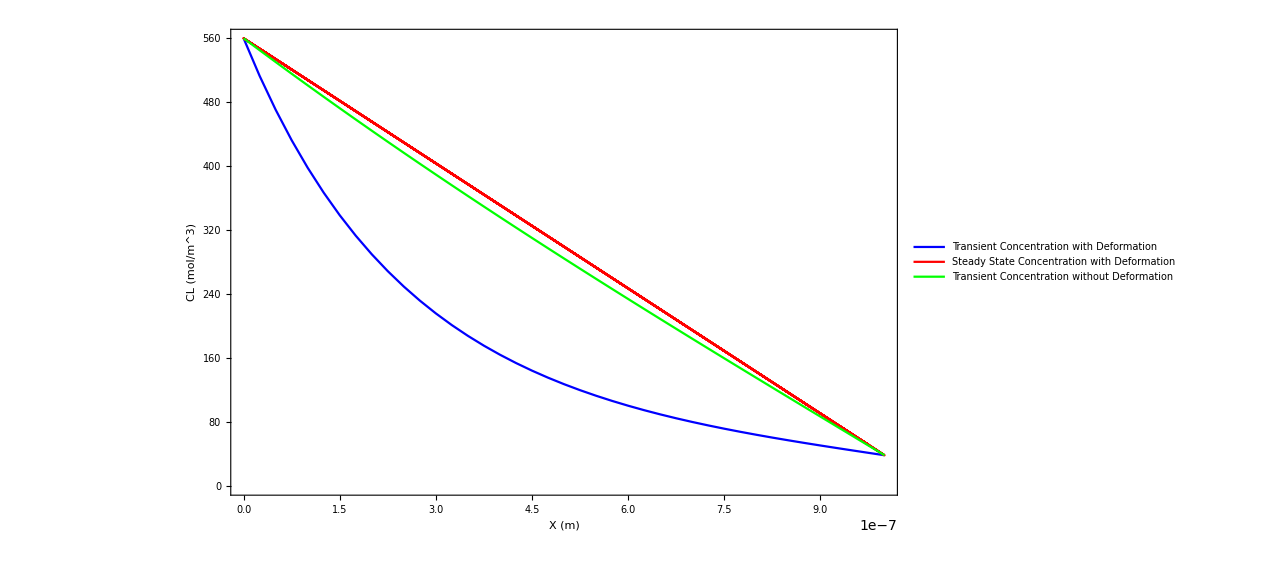

```mathematica
dataContentSteadyState=Import["/Users/glberge/SolidMechanics/SolidMechanicsExamples/LCM/blockDiffusionNew/blockDiffusionSteadyState_CL_displacement.txt","table"];

dataContentNoDeformation=Import["/Users/glberge/SolidMechanics/SolidMechanicsExamples/LCM/blockDiffusionNew/blockDiffusionTransient_CL_NoDisplacement.txt","table"];

SortedDataContentNoDeformation =Sort[dataContentNoDeformation[[1 ;;41,2]]];

Show[ListLinePlot[dataContent[[All,{1,2}]],PlotStyle -> Blue,PlotRange ->{{0.,1*10^-6},{0,560}}],

ListLinePlot[dataContentSteadyState[[All,{1,2}]],PlotStyle -> Red, PlotLegends -> 

Placed[LineLegend[{Blue,Red, Green},{"Transient Concentration with Deformation","Steady State Concentration with Deformation", "Transient Concentration without Deformation"}, LegendFunction-> Framed],{0.7,0.8}]],

ListLinePlot[Table[{dataContent[[i,1]],SortedDataContentNoDeformation[[i]]},{i,1,41}],PlotStyle -> Green],

AxesLabel-> {"X (m)","CL (mol/m^3)"}, Frame -> True]

SetOptions[ListLinePlot,BaseStyle->{FontFamily->"Helvetica",FontSize->16}];
```